# Classification in Machine Learning

## Code

```mathematica
PlotDecisionBoundry[data_, db_, xrange_, yrange_]:= Module[ 
	{dots, region},

	region = RegionPlot[{db>0, db<0},
				xrange,yrange, PlotStyle -> {Directive[Green,Opacity[.15]],Directive[Blue,Opacity[.25]]}];
	dots = ListPlot[data,PlotStyle->{Darker @ Green,Darker @ Blue}];
	Show[region, dots, FrameLabel->Style[#, 15]&/@(ToString[#]&/@{xrange[[1]],yrange[[1]]}),PlotRange->All]
]
```

### Logistic Regression

```mathematica
LogisticH[t_List, x_List]:=1/(1+ⅇ^(-t.Prepend[x, 1]))
```

```mathematica
LogReg[x_List,y_List]:= Module[
	{J, vars, t, ts},

	ts = Array[t,Length[Transpose@x]+1, 0];
	J[ts_]:= Sum[(LogisticH[ts, x[[i]]]-y[[i]])^2,{i, 1, Length[x]}];
	ts/.NMinimize[J[ts],ts][[2]]
]
```

```mathematica
mp[x_List,n_]:=Delete[(Times@@Power[x,#]&/@Flatten[Permutations/@(PadRight[#,Length@x]&)/@Flatten[IntegerPartitions[#,Length@x]&/@Range[0,n],1],1]),1]

advancedLogReg[x_List, y_List, deg_]:= Module[
	{J, vars, ts, f, ts2, newx},

	ts = Array[t,Length[Transpose@x]];
	vars = Array[X, Length[Transpose@x]];
	f[vars_,data_,n_]:=mp[vars,n]/.MapThread[#1->#2&,{vars,data}]
	ts2=Flatten@{1, mp[ts,deg]};
	newx = f[vars,#,2]&/@x;
	LogReg[newx,y].ts2
]
```

```mathematica
hypo[t_List,x_,i_]:=ⅇ^(t[[i]].Prepend[x, 1])/Sum[ⅇ^(t[[j]].Prepend[x, 1]),{j,1,Length[t]}]
nLogReg[x_List,y_List]:=Module[
	{l,ts},

	ts=Array[t,{Length@Union@y,Length[Transpose@x]+1}];
	l[ts]:=Sum[Log[hypo[ts,x⟦i⟧,y⟦i⟧]],{i, 1, Length[x]}];
	ts/.NMaximize[l[ts],Flatten@ts][[2]]
]
```

```mathematica
LogRegFunc[x_List,y_List]:=Module[
	{t, vars, k, list},

	k = Length@Transpose@x;
	vars = Array[u, k];
	t = nLogReg[x,y];
	list = #.Prepend[vars,1]&/@t
]
```

## An Iris Flower Example

```mathematica
irisAll=ExampleData[{"Statistics","FisherIris"}];
```

### Binary Classification

Let’s start from binary classification 
y ∈ {0, 1}   0 → versicolor 1→ virginica
x = (x_1, x_2)  
x_1→ sepal width,  x_2→ petal width

### Versicolor and Virginica

-Graphics- | -Graphics-

### Preprocess

```mathematica
iris=irisAll[[51;;150]]⟦All,{2,4,5}⟧;
m=Length[iris];
cut=Ceiling[0.8 m];
rs=RandomSample[Range@m];
train=iris⟦rs⟦1;;cut⟧⟧/.{"virginica"->0,"versicolor"->1};
test=iris⟦rs⟦cut+1;;-1⟧⟧/.{"virginica"->0,"versicolor"->1};
x=train⟦All,1;;2⟧;
y=train⟦All,-1⟧;
cate2n4=Partition[iris⟦All,1;;2⟧,50];
```

```mathematica
train1=Select[train,#[[3]]==1&];
train0=Select[train,#[[3]]==0&];
test1=Select[test,#[[3]]==1&];
test0=Select[test,#[[3]]==0&];
```

### 3D Visualization

```mathematica
pts3D=Graphics3D[{PointSize[0.02],{Darker@Green,Point/@train1,Darker@Blue,Point/@train0}}];
```

```mathematica
Manipulate[Show[Plot3D[1/(1+ⅇ^(θ0+θ1 x1+θ2 x2)),{x1,2,4},{x2,1,2.5},PlotStyle->Opacity[0.6],ColorFunction->Function[{x,y,z},RGBColor[0,z,1-z]],PerformanceGoal->"Quality",Mesh->None,AxesLabel->{x1,x2}],Plot3D[1/2,{x1,2,4},{x2,1,2.5},PlotStyle->{Gray,Opacity[0.6]},PerformanceGoal->"Quality",Mesh->None],pts3D,PlotRange->All,PlotLabel->1/(1+ⅇ^(θ0+θ1 x1+θ2 x2)),ImageSize->500],{θ0,-16,-15,Appearance->"Labeled"},{θ1,-3.2,-1.5,Appearance->"Labeled"},{θ2,12,14,Appearance->"Labeled"},ControlPlacement->Left]
```

### Maximizing Log-Likelihood

```mathematica
h[{x1_,x2_}]:=1/(1+ⅇ^(Subscript[θ, 0]+Subscript[θ, 1] x1+Subscript[θ, 2] x2))
```

```mathematica
loglikelihood=∑_(i=1)^Length[train] (Log[(1-y⟦i⟧)(1-h[x⟦i⟧])+y⟦i⟧h[x⟦i⟧]]);
```

```mathematica
soln2=NMaximize[loglikelihood,{Subscript[θ, 0],Subscript[θ, 1],Subscript[θ, 2]}]
```

{-9.1037,{θ_0→-17.3308,θ_1→-3.67018,θ_2→17.1599}}

```mathematica
coeff={Subscript[θ, 0],Subscript[θ, 1],Subscript[θ, 2]}/.soln2[[2]]
```

{-17.3308,-3.67018,17.1599}

```mathematica
decisionBoundary=coeff.{1,x1,x2}
```

-17.3308-3.67018 x1+17.1599 x2

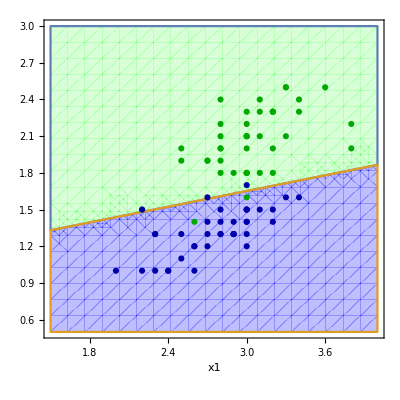

```mathematica
PlotDecisionBoundry[{train0[[All,1;;2]],train1[[All,1;;2]]},decisionBoundary,{x1,1.5,4},{x2,0.5,3}]
```

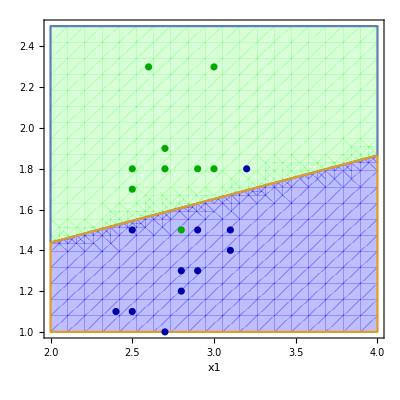

```mathematica
PlotDecisionBoundry[{test0[[All,1;;2]],test1[[All,1;;2]]},decisionBoundary,{x1,2,4},{x2,1,2.5}]
```

## Multi-class Classification

-Graphics- | -Graphics- | -Graphics-

#### Visualization

```mathematica
data=irisAll[[All,{2,4,5}]]/.{"setosa"->1,"virginica"->2,"versicolor"->3};
```

```mathematica
xvals=data[[All,{1,2}]];
yvals=data[[All,-1]];
```

```mathematica
Clear[h]
```

```mathematica
h[{x1_,x2_},k_]:=ⅇ^(Subscript[a, k]+Subscript[b, k] x1+Subscript[c, k] x2)/(ⅇ^(Subscript[a, 1]+Subscript[b, 1] x1+Subscript[c, 1] x2)+ⅇ^(Subscript[a, 2]+Subscript[b, 2] x1+Subscript[c, 2] x2)+ⅇ^(Subscript[a, 3]+Subscript[b, 3] x1+Subscript[c, 3] x2))
```

```mathematica
loglikelihood2=Sum[Log[h[xvals⟦i⟧,yvals⟦i⟧]],{i, 1, Length[xvals]}];
```

```mathematica
Flatten@Table[{Subscript[a, i],Subscript[b, i],Subscript[c, i]},{i,1,3}]
```

```mathematica
result=NMaximize[loglikelihood2,{Subscript[a, 1],Subscript[b, 1],Subscript[c, 1],Subscript[a, 2],Subscript[b, 2],Subscript[c, 2],Subscript[a, 3],Subscript[b, 3],Subscript[c, 3]}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-13.6995,{a_1→4.59327,b_1→15.9603,c_1→-30.2965,a_2→-7.54327,b_2→-1.24396,c_2→32.8702,a_3→6.83604,b_3→2.66314,c_3→17.17}}

```mathematica
{{Subscript[a, 1],Subscript[b, 1],Subscript[c, 1]},{Subscript[a, 2],Subscript[b, 2],Subscript[c, 2]},{Subscript[a, 3],Subscript[b, 3],Subscript[c, 3]}}/.result[[2]]
```

```mathematica
#.{1,x1,x2}&/@{{Subscript[a, 1],Subscript[b, 1],Subscript[c, 1]},{Subscript[a, 2],Subscript[b, 2],Subscript[c, 2]},{Subscript[a, 3],Subscript[b, 3],Subscript[c, 3]}}/.result[[2]]
```

{4.59327+15.9603 x1-30.2965 x2,-7.54327-1.24396 x1+32.8702 x2,6.83604+2.66314 x1+17.17 x2}

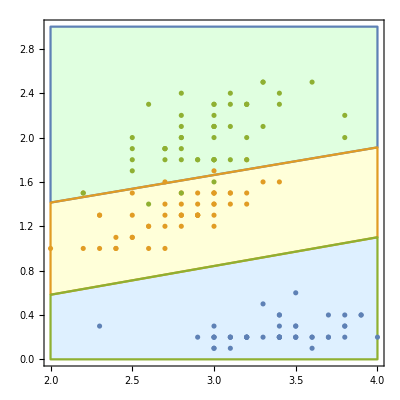

```mathematica
list=LogRegFunc[xvals,yvals];
dots3=ListPlot[Partition[data[[All,1;;2]],50]];
Show[RegionPlot[Evaluate@((First@#>Max@Rest@#)&/@(RotateLeft[list,#]&)/@Range@Length@list),{u[1],2,4},{u[2],0,3},PlotStyle->RotateLeft@{LightBlue,LightGreen,LightYellow}],dots3]
```